# Calculating mathematial constants using Monte Carlo simulations

Bhoris Dhanjal

## Section 1 : Pi

### Elementary Method

```mathematica
pairs=RandomReal[{-1,1},{10000,2}];
4 Count[Map[Norm,pairs],_?(#≤1&)]/10000.
```

3.1252

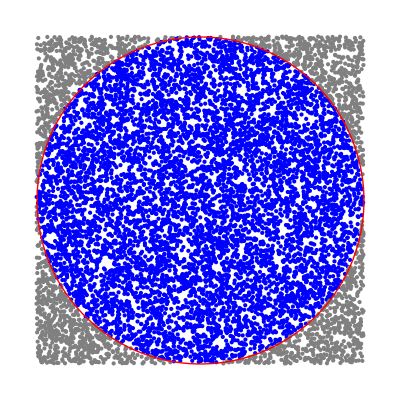

```mathematica
Graphics[{PointSize[Small],Blue,Point@Select[pairs,Norm[#]≤1&],Gray,Point@Select[pairs,Norm[#]>1&],Red,Thick,Circle[]},AspectRatio->1]
```

```mathematica
approxPi[n_]:=4. Count[Map[Norm,RandomReal[{-1,1},{n,2}]],_?(#≤1&)]/n
```

```mathematica
RepeatedExperiment=Table[approxPi[10^6],{10^3}];
```

```mathematica
Mean[RepeatedExperiment]
```

3.14151

```mathematica
NumberForm[3.1415106560000003,15]
```

3.141510656

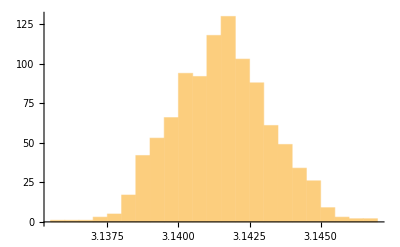

```mathematica
Histogram[RepeatedExperiment]
```

### Buffon' s Needle

```mathematica
BuffonsNeedle[r_,{x_,y_},n_]:=Module[
{
data=Table[{{x Random[Real],y Random[Real]},π Random[Real]},{n}],
lines,hits,misses
},
Graphics[lines=(Function[s,First[#]+s  r/2 Through[{Cos,Sin}[Last[#]]]]/@{1,-1})&/@data;
{
Line[{{#,0},{#,y}}]&/@Range[0,Ceiling[x]],
PointSize[.01],
{misses,hits}=Map[Last,Split[Sort[Transpose[{Abs[Subtract@@(Floor/@First/@#)&/@lines],lines}]],(First[#1]==First[#2]&)],{2}];
Transpose[{
{RGBColor[1,.47,0],RGBColor[.67,.75,.15]},
{Line/@#}&/@{hits,misses}
}]
}, PlotLabel-> Column[{
Style[
Row[{"hit ratio: ",ToString[TraditionalForm["hits"/"N"]]," = ",With[{a=Length[hits],b=n},HoldForm[a/b]]," ~~ ",ToString[Round[100Length[hits]/n]],"%"}],"Label"],
Style[
Row[{"π"," ~~ ",ToString[TraditionalForm[("2 x L x N")/"hits"]]," = ",With[{a=Length[hits],b=n, c=r},HoldForm[(2c b)/a]]," ~~ ",ToString[N[2n r/Length[hits]]]}],
"Label"]}],PlotRange->{{-1/2,x+1/2},{-1/2,y+1/2}},ImageSize->{400,300}]
];
```

```mathematica
Manipulate[SeedRandom[sr];BuffonsNeedle[length,{10,6},needles],{{needles,200,"number of needles (N)"},20,1000,1,Appearance-> "Labeled"},{{length,.6,"needle length (L)"},.25,1,Appearance-> "Labeled"},{{sr,12,"random seed"},1,100,1},SaveDefinitions->True]
```

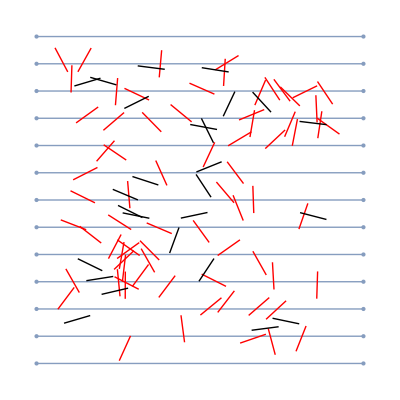

1.35135

```mathematica
d=0.2;n=100;
lines=MeshRegion[Join@@Table[{{-1-d,y},{1+d,y}},{y,-1-d,1+d,d}],Line[Partition[Range[2 Floor[2/d+3]],2]]];
needles=Table[Line[{pt,RandomPoint[Circle[pt,d]]}],{pt,RandomReal[{-1,1},{n,2}]}];
overlap=Select[needles,!RegionDisjoint[lines,#]&];
Show[lines,Graphics[{Red,overlap,Black,Complement[needles,overlap]}]]
N[( n)/Length[overlap]]
```

```mathematica
ComplexInfinity
```

```mathematica
RepeatedBuffon=Table[
d=0.2;n=10000;
lines=MeshRegion[Join@@Table[{{-1-d,y},{1+d,y}},{y,-1-d,1+d,d}],Line[Partition[Range[2 Floor[2/d+3]],2]]];
needles=Table[Line[{pt,RandomPoint[Circle[pt,d]]}],{pt,RandomReal[{-1,1},{n,2}]}];
overlap=Select[needles,!RegionDisjoint[lines,#]&];
N[(2 n)/Length[overlap]], {500}];
```

```mathematica
Mean[RepeatedBuffon]
```

3.14169

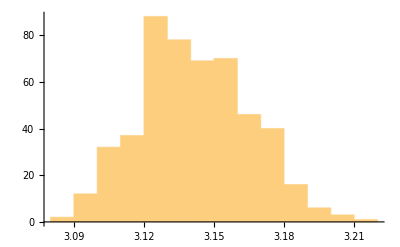

```mathematica
Histogram[RepeatedBuffon]
```

```mathematica
NewRepeatedBuffon=Table[d=0.2;n=10000;
lines=MeshRegion[Join@@Table[{{-1-d,y},{1+d,y}},{y,-1-d,1+d,d}],Line[Partition[Range[2 Floor[2/d+3]],2]]];
needles=Table[Line[{pt,RandomPoint[Circle[pt,0.5d]]}],{pt,RandomReal[{-1,1},{n,2}]}];
overlap=Select[needles,!RegionDisjoint[lines,#]&];
N[( n)/Length[overlap]], {500}];
```

```mathematica
Mean[NewRepeatedBuffon]
```

3.14413

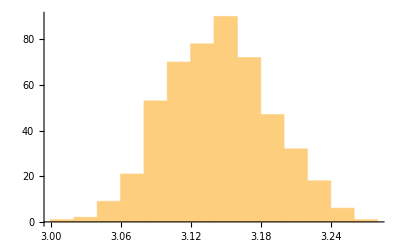

```mathematica
Histogram[NewRepeatedBuffon]
```

## Euler Mascheroni Constant

### Gumbel Distribution

```mathematica
approxgamma[n_]:=Mean[-Log[-Log[RandomReal[{0,1},{n}]]]]
```

```mathematica
approxgamma[10^6]
```

0.576802

```mathematica
RepeatedGammaExp=Table[approxgamma[10^6], {10^4}];
```

```mathematica
NumberForm[Mean[RepeatedGammaExp],15]
```

0.577210180043852

```mathematica
N[EulerGamma,15]
```

0.577215664901533

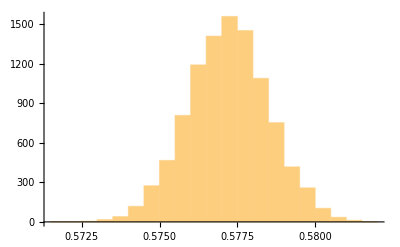

```mathematica
Histogram[RepeatedGammaExp]
```

## Exponential

```mathematica
N[Mean[Table[Module[{u=Random[],t=1},While[u<1,u=Random[]+u;t++];t],{10^6}]]]
```

2.71786

```mathematica
RepeatedExp[n_,repeat_]:=Table[Mean[Table[Module[{u=Random[],t=1},While[u<1,u=Random[]+u;t++];t],{n}]],{repeat}]
```

```mathematica
RepeatedData=RepeatedExp[10^6,1000];
```

```mathematica
N[Mean[RepeatedData],10]
```

2.718262161

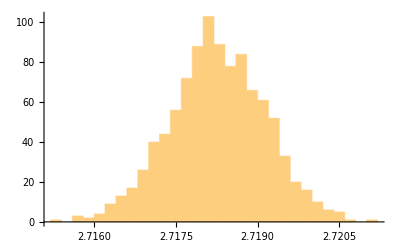

```mathematica
Histogram[RepeatedData]
```

## Numerical Integration

```mathematica
g[x_]=1/Log[x];
```

```mathematica
a=2;b=5;
```

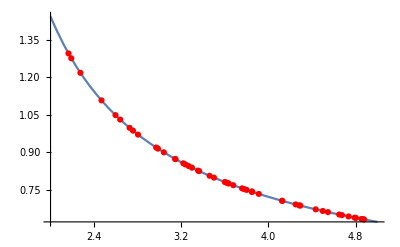

```mathematica
ExampleRand=RandomReal[{2,5},{50}];
ExamplePoints=g[ExampleRand];
Show[Plot[g[x],{x,2,5}],ListPlot[Transpose[{ExampleRand,ExamplePoints}],PlotStyle->{Red}]]
```

```mathematica
RepeatedIntegral[points_,repeat_]:=Table[N[(b-a)/(points-1)Total[g[RandomReal[{a,b},{points}]]]],{repeat}]
```

```mathematica
IntegralData:=RepeatedIntegral[10^6,1000]
```

```mathematica
Mean[IntegralData]
```

2.58942

```mathematica
NIntegrate[g[x],{x,2,5}]
```

2.58942

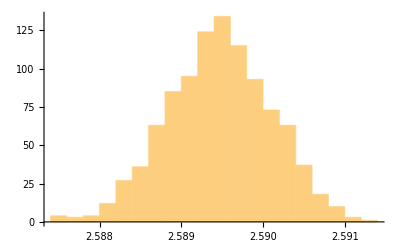

```mathematica
Histogram[IntegralData]
```